# Functional Programming

Peter Cullen Burbery

Abstract

## Creating Functions

## Basic Examples of Functional Programming

### Function

XXXX:

```mathematica
Function[u,3+u][x]
```

3+x

```mathematica
Function[u,3+u][x]
```

3+x

```mathematica
Function[3+#][x]
```

3+x

```mathematica
(3+#)&[x]
```

3+x

```mathematica
Function[{u,v},u^2+v^4][x,y]
```

x^2+y^4

```mathematica
(#1^2+#2^4)&[x,y]
```

x^2+y^4

```mathematica
f=(3+#)&
```

3+#1&

```mathematica
{f[a],f[b]}
```

{3+a,3+b}

```mathematica
f[#u,#v,#u]&[<|"u"->x,"v"->y|>]
```

3+x

This might be a bug. The documentation says the output is f[x,y,x].

### Slot

```mathematica
f[#,a,#,b]&[x,y]
```

f[x,a,x,b]

```mathematica
f[#1,#2,#1,#3]&[x,y,z]
```

f[x,y,x,z]

```mathematica
f[#u,#v,#u]&[<|"u"->x,"v"->y|>]
```

f[x,y,x]

### SlotSequence

```mathematica
ClearAll[f]
```

```mathematica
f[x,##,y,##]&[a,b,c,d]
```

f[x,a,b,c,d,y,a,b,c,d]

```mathematica
f[##2]&[a,b,c,d]
```

f[b,c,d]

```mathematica
f[##3]&[a,b,c,d]
```

f[c,d]

```mathematica
f[##4]&[a,b,c,d]
```

f[d]

## Neat Examples

### Function

```mathematica
r[g_,h_]=If[#1==0,g[##2],h[#0[#1-1,##2],#1-1,##2]]&
```

If[#1==0,g[##2],h[#0[#1-1,##2],#1-1,##2]]&

```mathematica
r[1&,#1(#2+1)&][10]
```

3628800

```mathematica
r[1&,#1(#2+1)&][100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
NewtonZero[f_,x0_]:=FixedPoint[#-f[#]/f'[#]&,x0]
```

```mathematica
NewtonZero[BesselJ[2,#]&,5.0]
```

5.13562

```mathematica
NewtonZero[BesselJ[2,#]&,718.]
```

718.637

### Slot

```mathematica
f=If[#1==1,1,#1 #0[#1-1]]&
```

If[#1==1,1,#1 #0[#1-1]]&

```mathematica
f[10]
```

3628800

```mathematica
10!
```

3628800

## Applying Functions to Lists

## Basic Examples

### Map

XXXX:

```mathematica
Map[f,{a,b,c,d,e}]
```

{f[a],f[b],f[c],f[d],f[e]}

Alternative input form:

```mathematica
f/@{a,b,c,d,e}
```

{f[a],f[b],f[c],f[d],f[e]}

```mathematica
(1+g[#])&/@{a,b,c,d,e}
```

{1+g[a],1+g[b],1+g[c],1+g[d],1+g[e]}

```mathematica
Function[x,x^2]/@{1,2,3,4}
```

{1,4,9,16}

Map at top level:

```mathematica
ExpressionTree[{{a,b},{c,d,e}}]
```

-Graphics-

```mathematica
Map[f,{{a,b},{c,d,e}}]
```

{f[{a,b}],f[{c,d,e}]}

```mathematica
ExpressionTree[Map[f,{{a,b},{c,d,e}}]]
```

-Graphics-

Map at level 2:

```mathematica
Map[f,{{a,b},{c,d,e}},{2}]
```

{{f[a],f[b]},{f[c],f[d],f[e]}}

```mathematica
ExpressionTree[Map[f,{{a,b},{c,d,e}},{2}]]
```

-Graphics-

Map at levels 1 and 2:

```mathematica
Map[f,{{a,b},{c,d,e}},2]
```

{f[{f[a],f[b]}],f[{f[c],f[d],f[e]}]}

```mathematica
ExpressionTree[Map[f,{{a,b},{c,d,e}},2]]
```

-Graphics-

Test a depth tree expression:

```mathematica
PersistResourceFunction["SymbolicIndexedArray"]
```

Success[…]

```mathematica
EXPRESSION=SymbolicIndexedArray[x,{3,3,3}]
```

{{{x111,x112,x113},{x121,x122,x123},{x131,x132,x133}},{{x211,x212,x213},{x221,x222,x223},{x231,x232,x233}},{{x311,x312,x313},{x321,x322,x323},{x331,x332,x333}}}

```mathematica
ExpressionTree[EXPRESSION]
```

-Graphics-

```mathematica
RootTree[ExpressionTree[EXPRESSION],3]
```

-Graphics-

```mathematica
RootTree[ExpressionTree[EXPRESSION],2]
```

-Graphics-

```mathematica
RootTree[ExpressionTree[EXPRESSION],3]
```

-Graphics-

```mathematica
Map[f,EXPRESSION]
```

{f[{{x111,x112,x113},{x121,x122,x123},{x131,x132,x133}}],f[{{x211,x212,x213},{x221,x222,x223},{x231,x232,x233}}],f[{{x311,x312,x313},{x321,x322,x323},{x331,x332,x333}}]}

```mathematica
RootTree[ExpressionTree[Map[f,EXPRESSION]],4]
```

-Graphics-

```mathematica
RootTree[ExpressionTree[Map[f,EXPRESSION,{2}]],4]
```

-Graphics-

```mathematica
RootTree[ExpressionTree[Map[f,EXPRESSION,{3}]],4]
```

-Graphics-

```mathematica
RootTree[ExpressionTree[Map[f,EXPRESSION,Infinity]],5]
```

-Graphics-

```mathematica
RootTree[ExpressionTree[Map[f,EXPRESSION,{2,3}]],5]
```

-Graphics-

Use the map operator:

```mathematica
Map[f][{a,b,c,d}]
```

{f[a],f[b],f[c],f[d]}

Map over an association:

```mathematica
Map[h,<|a->b,c->d|>]
```

<|a→h[b],c→h[d]|>

Map at the second level of a nested Association:

```mathematica
Map[h,<|a-><|b->c|>,d->{<|e->f|>}|>,{1,3}]
```

<|a→h[<|b→h[c]|>],d→h[{h[<|e→h[f]|>]}]|>

### Apply

```mathematica
Apply[f,{a,b,c,d}]
```

f[a,b,c,d]

```mathematica
f@@{a,b,c,d}
```

f[a,b,c,d]

```mathematica
Plus@@{a,b,c,d}
```

a+b+c+d

```mathematica
f@@{{a,b},{c},d}
```

f[{a,b},{c},d]

Use the operator form of Apply:

```mathematica
Apply[f][{{a,b},{c},d}]
```

f[{a,b},{c},d]

Apply f to an Association:

```mathematica
Apply[f,<|1->a,2->b,3->c|>]
```

f[a,b,c]

Applying a List to an association is equivalent to using Values:

```mathematica
Apply[List,<|1->a,2->b,3->c,4->{d}|>]
```

{a,b,c,{d}}

```mathematica
Values[<|1->a,2->b,3->c,4->{d}|>]
```

{a,b,c,{d}}

Apply f at the second level:

```mathematica
Apply[List,<|1->a,2->b,3->c,4->{d,{e}}|>,{2}]
```

<|1→a,2→b,3→c,4→{d,{e}}|>

Apply f at several levels:

```mathematica
Apply[List,<|1->a,2->b,3->c,4->{d,{e}}|>,{0,2}]
```

{a,b,c,{d,{e}}}

### MapApply

```mathematica
MapApply[f,{{a,b},{c,d}}]
```

{f[a,b],f[c,d]}

```mathematica
f@@@{{a,b},{c,d}}
```

{f[a,b],f[c,d]}

Sum sublists by replacing the head of each with Plus:

```mathematica
Plus@@@{{a,b,c,d},{1,2,3,4},{e,f,5,6}}
```

{a+b+c+d,10,11+e+f}

```mathematica
Times@@@{{a,b,c,d},{1,2,3,4},{e,f,5,6}}
```

{a b c d,24,30 e f}

Use the operator form of MapApply:

```mathematica
MapApply[f][{{a,b},{c},{d,e}}]
```

{f[a,b],f[c],f[d,e]}

MapApply only affects the values of an association:

```mathematica
MapApply[f,<|{1,2}->{a},{3,4}->{c,d,e}|>]
```

<|{1,2}→f[a],{3,4}→f[c,d,e]|>

### MapIndexed

```mathematica
MapIndexed[f,{a,b,c,d}]
```

{f[a,{1}],f[b,{2}],f[c,{3}],f[d,{4}]}

#2 gives the indices of each part:

```mathematica
MapIndexed[First[#2]+f[#1]&,{a,b,c,d}]
```

{1+f[a],2+f[b],3+f[c],4+f[d]}

```mathematica
MapIndexed[First[#2]f[#1]&,{a,b,c,d}]
```

{f[a],2 f[b],3 f[c],4 f[d]}

```mathematica
MapIndexed[First[#2]f[#1]&,Range[4]]
```

{f[1],2 f[2],3 f[3],4 f[4]}

```mathematica
MapIndexed[First[#2]f[#1]&,Range[20]]
```

{f[1],2 f[2],3 f[3],4 f[4],5 f[5],6 f[6],7 f[7],8 f[8],9 f[9],10 f[10],11 f[11],12 f[12],13 f[13],14 f[14],15 f[15],16 f[16],17 f[17],18 f[18],19 f[19],20 f[20]}

```mathematica
MapIndexed[First[#2]f[#1]&,Range[100,120]]
```

{f[100],2 f[101],3 f[102],4 f[103],5 f[104],6 f[105],7 f[106],8 f[107],9 f[108],10 f[109],11 f[110],12 f[111],13 f[112],14 f[113],15 f[114],16 f[115],17 f[116],18 f[117],19 f[118],20 f[119],21 f[120]}

```mathematica
MapIndexed[f,{{a,b},{c,d,e}}]
```

{f[{a,b},{1}],f[{c,d,e},{2}]}

```mathematica
MapIndexed[f,{{a,b},{c,d,e}},{2}]
```

{{f[a,{1,1}],f[b,{1,2}]},{f[c,{2,1}],f[d,{2,2}],f[e,{2,3}]}}

Map over an association:

```mathematica
MapIndexed[f,<|"a"->1,a->2,1->1|>]
```

<|a→f[1,{Key[a]}],a→f[2,{Key[a]}],1→f[1,{Key[1]}]|>

### MapThread

Apply f to corresponding pairs of elements:

```mathematica
MapThread[f,{{a,b,c},{x,y,z}}]
```

{f[a,x],f[b,y],f[c,z]}

Apply f to elements of a matrix:

```mathematica
MapThread[f,{{{a,b},{c,d}},{{u,v},{s,t}}},2]
```

{{f[a,u],f[b,v]},{f[c,s],f[d,t]}}

Apply f to corresponding values of associations:

```mathematica
MapThread[f,{<|a->1|>,<|a->1|>}]
```

<|a→f[1,1]|>

Use the operator form of MapThread:

```mathematica
MapThread[f][{{a,b,c,d},{1,2,3,4}}]
```

{f[a,1],f[b,2],f[c,3],f[d,4]}

### MapAt

Map f onto the part at position 2:

```mathematica
MapAt[f,{a,b,c,d},2]
```

{a,f[b],c,d}

Map f onto multiple parts:

```mathematica
MapAt[f,{a,b,c,d},{{1},{4}}]
```

{f[a],b,c,f[d]}

Map f onto a more deeply nested part:

```mathematica
MapAt[f,{{a,b,c},{d,e}},{2,1}]
```

{{a,b,c},{f[d],e}}

## Applications

### Map

Reverse all sublists:

```mathematica
Reverse/@{{a,b},{c,d},{e,f}}
```

{{b,a},{d,c},{f,e}}

Add the same vector to every vector in a list:

```mathematica
Map[(#+{x,y})&,{{1,1},{2,2},{3,3},{4,4}}]
```

{{1+x,1+y},{2+x,2+y},{3+x,3+y},{4+x,4+y}}

Use Threaded:

```mathematica
Threaded[{x,y}]+{{1,1},{2,2},{3,3},{4,4}}
```

{{1+x,1+y},{2+x,2+y},{3+x,3+y},{4+x,4+y}}

```mathematica
{{1,1},{2,2},{3,3},{4,4}}+Threaded[{x,y}]
```

{{1+x,1+y},{2+x,2+y},{3+x,3+y},{4+x,4+y}}

Frame integers that are prime:

```mathematica
If[PrimeQ[#],Framed[#],#]&/@Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Make a grid:

```mathematica
If[PrimeQ[#],Framed[#],#]&/@Range[148]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148}

```mathematica
Partition[If[PrimeQ[#],Framed[#],#]&/@Range[148],UpTo[10]]
```

{{1,2,3,4,5,6,7,8,9,10},{11,12,13,14,15,16,17,18,19,20},{21,22,23,24,25,26,27,28,29,30},{31,32,33,34,35,36,37,38,39,40},{41,42,43,44,45,46,47,48,49,50},{51,52,53,54,55,56,57,58,59,60},{61,62,63,64,65,66,67,68,69,70},{71,72,73,74,75,76,77,78,79,80},{81,82,83,84,85,86,87,88,89,90},{91,92,93,94,95,96,97,98,99,100},{101,102,103,104,105,106,107,108,109,110},{111,112,113,114,115,116,117,118,119,120},{121,122,123,124,125,126,127,128,129,130},{131,132,133,134,135,136,137,138,139,140},{141,142,143,144,145,146,147,148}}

```mathematica
Multicolumn[If[PrimeQ[#],Framed[#],#]&/@Range[148]]
```

1 | 13 | 25 | 37 | 49 | 61 | 73 | 85 | 97 | 109 | 121 | 133 | 145
2 | 14 | 26 | 38 | 50 | 62 | 74 | 86 | 98 | 110 | 122 | 134 | 146
3 | 15 | 27 | 39 | 51 | 63 | 75 | 87 | 99 | 111 | 123 | 135 | 147
4 | 16 | 28 | 40 | 52 | 64 | 76 | 88 | 100 | 112 | 124 | 136 | 148
5 | 17 | 29 | 41 | 53 | 65 | 77 | 89 | 101 | 113 | 125 | 137 | 
6 | 18 | 30 | 42 | 54 | 66 | 78 | 90 | 102 | 114 | 126 | 138 | 
7 | 19 | 31 | 43 | 55 | 67 | 79 | 91 | 103 | 115 | 127 | 139 | 
8 | 20 | 32 | 44 | 56 | 68 | 80 | 92 | 104 | 116 | 128 | 140 | 
9 | 21 | 33 | 45 | 57 | 69 | 81 | 93 | 105 | 117 | 129 | 141 | 
10 | 22 | 34 | 46 | 58 | 70 | 82 | 94 | 106 | 118 | 130 | 142 | 
11 | 23 | 35 | 47 | 59 | 71 | 83 | 95 | 107 | 119 | 131 | 143 | 
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144 |

```mathematica
Multicolumn[If[PrimeQ[#],Framed[#],#]&/@Range[403]]
```

1 | 21 | 41 | 61 | 81 | 101 | 121 | 141 | 161 | 181 | 201 | 221 | 241 | 261 | 281 | 301 | 321 | 341 | 361 | 381 | 401
2 | 22 | 42 | 62 | 82 | 102 | 122 | 142 | 162 | 182 | 202 | 222 | 242 | 262 | 282 | 302 | 322 | 342 | 362 | 382 | 402
3 | 23 | 43 | 63 | 83 | 103 | 123 | 143 | 163 | 183 | 203 | 223 | 243 | 263 | 283 | 303 | 323 | 343 | 363 | 383 | 403
4 | 24 | 44 | 64 | 84 | 104 | 124 | 144 | 164 | 184 | 204 | 224 | 244 | 264 | 284 | 304 | 324 | 344 | 364 | 384 | 
5 | 25 | 45 | 65 | 85 | 105 | 125 | 145 | 165 | 185 | 205 | 225 | 245 | 265 | 285 | 305 | 325 | 345 | 365 | 385 | 
6 | 26 | 46 | 66 | 86 | 106 | 126 | 146 | 166 | 186 | 206 | 226 | 246 | 266 | 286 | 306 | 326 | 346 | 366 | 386 | 
7 | 27 | 47 | 67 | 87 | 107 | 127 | 147 | 167 | 187 | 207 | 227 | 247 | 267 | 287 | 307 | 327 | 347 | 367 | 387 | 
8 | 28 | 48 | 68 | 88 | 108 | 128 | 148 | 168 | 188 | 208 | 228 | 248 | 268 | 288 | 308 | 328 | 348 | 368 | 388 | 
9 | 29 | 49 | 69 | 89 | 109 | 129 | 149 | 169 | 189 | 209 | 229 | 249 | 269 | 289 | 309 | 329 | 349 | 369 | 389 | 
10 | 30 | 50 | 70 | 90 | 110 | 130 | 150 | 170 | 190 | 210 | 230 | 250 | 270 | 290 | 310 | 330 | 350 | 370 | 390 | 
11 | 31 | 51 | 71 | 91 | 111 | 131 | 151 | 171 | 191 | 211 | 231 | 251 | 271 | 291 | 311 | 331 | 351 | 371 | 391 | 
12 | 32 | 52 | 72 | 92 | 112 | 132 | 152 | 172 | 192 | 212 | 232 | 252 | 272 | 292 | 312 | 332 | 352 | 372 | 392 | 
13 | 33 | 53 | 73 | 93 | 113 | 133 | 153 | 173 | 193 | 213 | 233 | 253 | 273 | 293 | 313 | 333 | 353 | 373 | 393 | 
14 | 34 | 54 | 74 | 94 | 114 | 134 | 154 | 174 | 194 | 214 | 234 | 254 | 274 | 294 | 314 | 334 | 354 | 374 | 394 | 
15 | 35 | 55 | 75 | 95 | 115 | 135 | 155 | 175 | 195 | 215 | 235 | 255 | 275 | 295 | 315 | 335 | 355 | 375 | 395 | 
16 | 36 | 56 | 76 | 96 | 116 | 136 | 156 | 176 | 196 | 216 | 236 | 256 | 276 | 296 | 316 | 336 | 356 | 376 | 396 | 
17 | 37 | 57 | 77 | 97 | 117 | 137 | 157 | 177 | 197 | 217 | 237 | 257 | 277 | 297 | 317 | 337 | 357 | 377 | 397 | 
18 | 38 | 58 | 78 | 98 | 118 | 138 | 158 | 178 | 198 | 218 | 238 | 258 | 278 | 298 | 318 | 338 | 358 | 378 | 398 | 
19 | 39 | 59 | 79 | 99 | 119 | 139 | 159 | 179 | 199 | 219 | 239 | 259 | 279 | 299 | 319 | 339 | 359 | 379 | 399 | 
20 | 40 | 60 | 80 | 100 | 120 | 140 | 160 | 180 | 200 | 220 | 240 | 260 | 280 | 300 | 320 | 340 | 360 | 380 | 400 |

```mathematica
Multicolumn[If[PrimeQ[#],Framed[#],#]&/@Range[1096]]
```

1 | 34 | 67 | 100 | 133 | 166 | 199 | 232 | 265 | 298 | 331 | 364 | 397 | 430 | 463 | 496 | 529 | 562 | 595 | 628 | 661 | 694 | 727 | 760 | 793 | 826 | 859 | 892 | 925 | 958 | 991 | 1024 | 1057 | 1090
2 | 35 | 68 | 101 | 134 | 167 | 200 | 233 | 266 | 299 | 332 | 365 | 398 | 431 | 464 | 497 | 530 | 563 | 596 | 629 | 662 | 695 | 728 | 761 | 794 | 827 | 860 | 893 | 926 | 959 | 992 | 1025 | 1058 | 1091
3 | 36 | 69 | 102 | 135 | 168 | 201 | 234 | 267 | 300 | 333 | 366 | 399 | 432 | 465 | 498 | 531 | 564 | 597 | 630 | 663 | 696 | 729 | 762 | 795 | 828 | 861 | 894 | 927 | 960 | 993 | 1026 | 1059 | 1092
4 | 37 | 70 | 103 | 136 | 169 | 202 | 235 | 268 | 301 | 334 | 367 | 400 | 433 | 466 | 499 | 532 | 565 | 598 | 631 | 664 | 697 | 730 | 763 | 796 | 829 | 862 | 895 | 928 | 961 | 994 | 1027 | 1060 | 1093
5 | 38 | 71 | 104 | 137 | 170 | 203 | 236 | 269 | 302 | 335 | 368 | 401 | 434 | 467 | 500 | 533 | 566 | 599 | 632 | 665 | 698 | 731 | 764 | 797 | 830 | 863 | 896 | 929 | 962 | 995 | 1028 | 1061 | 1094
6 | 39 | 72 | 105 | 138 | 171 | 204 | 237 | 270 | 303 | 336 | 369 | 402 | 435 | 468 | 501 | 534 | 567 | 600 | 633 | 666 | 699 | 732 | 765 | 798 | 831 | 864 | 897 | 930 | 963 | 996 | 1029 | 1062 | 1095
7 | 40 | 73 | 106 | 139 | 172 | 205 | 238 | 271 | 304 | 337 | 370 | 403 | 436 | 469 | 502 | 535 | 568 | 601 | 634 | 667 | 700 | 733 | 766 | 799 | 832 | 865 | 898 | 931 | 964 | 997 | 1030 | 1063 | 1096
8 | 41 | 74 | 107 | 140 | 173 | 206 | 239 | 272 | 305 | 338 | 371 | 404 | 437 | 470 | 503 | 536 | 569 | 602 | 635 | 668 | 701 | 734 | 767 | 800 | 833 | 866 | 899 | 932 | 965 | 998 | 1031 | 1064 | 
9 | 42 | 75 | 108 | 141 | 174 | 207 | 240 | 273 | 306 | 339 | 372 | 405 | 438 | 471 | 504 | 537 | 570 | 603 | 636 | 669 | 702 | 735 | 768 | 801 | 834 | 867 | 900 | 933 | 966 | 999 | 1032 | 1065 | 
10 | 43 | 76 | 109 | 142 | 175 | 208 | 241 | 274 | 307 | 340 | 373 | 406 | 439 | 472 | 505 | 538 | 571 | 604 | 637 | 670 | 703 | 736 | 769 | 802 | 835 | 868 | 901 | 934 | 967 | 1000 | 1033 | 1066 | 
11 | 44 | 77 | 110 | 143 | 176 | 209 | 242 | 275 | 308 | 341 | 374 | 407 | 440 | 473 | 506 | 539 | 572 | 605 | 638 | 671 | 704 | 737 | 770 | 803 | 836 | 869 | 902 | 935 | 968 | 1001 | 1034 | 1067 | 
12 | 45 | 78 | 111 | 144 | 177 | 210 | 243 | 276 | 309 | 342 | 375 | 408 | 441 | 474 | 507 | 540 | 573 | 606 | 639 | 672 | 705 | 738 | 771 | 804 | 837 | 870 | 903 | 936 | 969 | 1002 | 1035 | 1068 | 
13 | 46 | 79 | 112 | 145 | 178 | 211 | 244 | 277 | 310 | 343 | 376 | 409 | 442 | 475 | 508 | 541 | 574 | 607 | 640 | 673 | 706 | 739 | 772 | 805 | 838 | 871 | 904 | 937 | 970 | 1003 | 1036 | 1069 | 
14 | 47 | 80 | 113 | 146 | 179 | 212 | 245 | 278 | 311 | 344 | 377 | 410 | 443 | 476 | 509 | 542 | 575 | 608 | 641 | 674 | 707 | 740 | 773 | 806 | 839 | 872 | 905 | 938 | 971 | 1004 | 1037 | 1070 | 
15 | 48 | 81 | 114 | 147 | 180 | 213 | 246 | 279 | 312 | 345 | 378 | 411 | 444 | 477 | 510 | 543 | 576 | 609 | 642 | 675 | 708 | 741 | 774 | 807 | 840 | 873 | 906 | 939 | 972 | 1005 | 1038 | 1071 | 
16 | 49 | 82 | 115 | 148 | 181 | 214 | 247 | 280 | 313 | 346 | 379 | 412 | 445 | 478 | 511 | 544 | 577 | 610 | 643 | 676 | 709 | 742 | 775 | 808 | 841 | 874 | 907 | 940 | 973 | 1006 | 1039 | 1072 | 
17 | 50 | 83 | 116 | 149 | 182 | 215 | 248 | 281 | 314 | 347 | 380 | 413 | 446 | 479 | 512 | 545 | 578 | 611 | 644 | 677 | 710 | 743 | 776 | 809 | 842 | 875 | 908 | 941 | 974 | 1007 | 1040 | 1073 | 
18 | 51 | 84 | 117 | 150 | 183 | 216 | 249 | 282 | 315 | 348 | 381 | 414 | 447 | 480 | 513 | 546 | 579 | 612 | 645 | 678 | 711 | 744 | 777 | 810 | 843 | 876 | 909 | 942 | 975 | 1008 | 1041 | 1074 | 
19 | 52 | 85 | 118 | 151 | 184 | 217 | 250 | 283 | 316 | 349 | 382 | 415 | 448 | 481 | 514 | 547 | 580 | 613 | 646 | 679 | 712 | 745 | 778 | 811 | 844 | 877 | 910 | 943 | 976 | 1009 | 1042 | 1075 | 
20 | 53 | 86 | 119 | 152 | 185 | 218 | 251 | 284 | 317 | 350 | 383 | 416 | 449 | 482 | 515 | 548 | 581 | 614 | 647 | 680 | 713 | 746 | 779 | 812 | 845 | 878 | 911 | 944 | 977 | 1010 | 1043 | 1076 | 
21 | 54 | 87 | 120 | 153 | 186 | 219 | 252 | 285 | 318 | 351 | 384 | 417 | 450 | 483 | 516 | 549 | 582 | 615 | 648 | 681 | 714 | 747 | 780 | 813 | 846 | 879 | 912 | 945 | 978 | 1011 | 1044 | 1077 | 
22 | 55 | 88 | 121 | 154 | 187 | 220 | 253 | 286 | 319 | 352 | 385 | 418 | 451 | 484 | 517 | 550 | 583 | 616 | 649 | 682 | 715 | 748 | 781 | 814 | 847 | 880 | 913 | 946 | 979 | 1012 | 1045 | 1078 | 
23 | 56 | 89 | 122 | 155 | 188 | 221 | 254 | 287 | 320 | 353 | 386 | 419 | 452 | 485 | 518 | 551 | 584 | 617 | 650 | 683 | 716 | 749 | 782 | 815 | 848 | 881 | 914 | 947 | 980 | 1013 | 1046 | 1079 | 
24 | 57 | 90 | 123 | 156 | 189 | 222 | 255 | 288 | 321 | 354 | 387 | 420 | 453 | 486 | 519 | 552 | 585 | 618 | 651 | 684 | 717 | 750 | 783 | 816 | 849 | 882 | 915 | 948 | 981 | 1014 | 1047 | 1080 | 
25 | 58 | 91 | 124 | 157 | 190 | 223 | 256 | 289 | 322 | 355 | 388 | 421 | 454 | 487 | 520 | 553 | 586 | 619 | 652 | 685 | 718 | 751 | 784 | 817 | 850 | 883 | 916 | 949 | 982 | 1015 | 1048 | 1081 | 
26 | 59 | 92 | 125 | 158 | 191 | 224 | 257 | 290 | 323 | 356 | 389 | 422 | 455 | 488 | 521 | 554 | 587 | 620 | 653 | 686 | 719 | 752 | 785 | 818 | 851 | 884 | 917 | 950 | 983 | 1016 | 1049 | 1082 | 
27 | 60 | 93 | 126 | 159 | 192 | 225 | 258 | 291 | 324 | 357 | 390 | 423 | 456 | 489 | 522 | 555 | 588 | 621 | 654 | 687 | 720 | 753 | 786 | 819 | 852 | 885 | 918 | 951 | 984 | 1017 | 1050 | 1083 | 
28 | 61 | 94 | 127 | 160 | 193 | 226 | 259 | 292 | 325 | 358 | 391 | 424 | 457 | 490 | 523 | 556 | 589 | 622 | 655 | 688 | 721 | 754 | 787 | 820 | 853 | 886 | 919 | 952 | 985 | 1018 | 1051 | 1084 | 
29 | 62 | 95 | 128 | 161 | 194 | 227 | 260 | 293 | 326 | 359 | 392 | 425 | 458 | 491 | 524 | 557 | 590 | 623 | 656 | 689 | 722 | 755 | 788 | 821 | 854 | 887 | 920 | 953 | 986 | 1019 | 1052 | 1085 | 
30 | 63 | 96 | 129 | 162 | 195 | 228 | 261 | 294 | 327 | 360 | 393 | 426 | 459 | 492 | 525 | 558 | 591 | 624 | 657 | 690 | 723 | 756 | 789 | 822 | 855 | 888 | 921 | 954 | 987 | 1020 | 1053 | 1086 | 
31 | 64 | 97 | 130 | 163 | 196 | 229 | 262 | 295 | 328 | 361 | 394 | 427 | 460 | 493 | 526 | 559 | 592 | 625 | 658 | 691 | 724 | 757 | 790 | 823 | 856 | 889 | 922 | 955 | 988 | 1021 | 1054 | 1087 | 
32 | 65 | 98 | 131 | 164 | 197 | 230 | 263 | 296 | 329 | 362 | 395 | 428 | 461 | 494 | 527 | 560 | 593 | 626 | 659 | 692 | 725 | 758 | 791 | 824 | 857 | 890 | 923 | 956 | 989 | 1022 | 1055 | 1088 | 
33 | 66 | 99 | 132 | 165 | 198 | 231 | 264 | 297 | 330 | 363 | 396 | 429 | 462 | 495 | 528 | 561 | 594 | 627 | 660 | 693 | 726 | 759 | 792 | 825 | 858 | 891 | 924 | 957 | 990 | 1023 | 1056 | 1089 |

```mathematica
Multicolumn[If[EvenQ[#],Style[#,Background->Yellow],Style[#,Background->LightGray]]&/@Range[403]]
```

1 | 21 | 41 | 61 | 81 | 101 | 121 | 141 | 161 | 181 | 201 | 221 | 241 | 261 | 281 | 301 | 321 | 341 | 361 | 381 | 401
2 | 22 | 42 | 62 | 82 | 102 | 122 | 142 | 162 | 182 | 202 | 222 | 242 | 262 | 282 | 302 | 322 | 342 | 362 | 382 | 402
3 | 23 | 43 | 63 | 83 | 103 | 123 | 143 | 163 | 183 | 203 | 223 | 243 | 263 | 283 | 303 | 323 | 343 | 363 | 383 | 403
4 | 24 | 44 | 64 | 84 | 104 | 124 | 144 | 164 | 184 | 204 | 224 | 244 | 264 | 284 | 304 | 324 | 344 | 364 | 384 | 
5 | 25 | 45 | 65 | 85 | 105 | 125 | 145 | 165 | 185 | 205 | 225 | 245 | 265 | 285 | 305 | 325 | 345 | 365 | 385 | 
6 | 26 | 46 | 66 | 86 | 106 | 126 | 146 | 166 | 186 | 206 | 226 | 246 | 266 | 286 | 306 | 326 | 346 | 366 | 386 | 
7 | 27 | 47 | 67 | 87 | 107 | 127 | 147 | 167 | 187 | 207 | 227 | 247 | 267 | 287 | 307 | 327 | 347 | 367 | 387 | 
8 | 28 | 48 | 68 | 88 | 108 | 128 | 148 | 168 | 188 | 208 | 228 | 248 | 268 | 288 | 308 | 328 | 348 | 368 | 388 | 
9 | 29 | 49 | 69 | 89 | 109 | 129 | 149 | 169 | 189 | 209 | 229 | 249 | 269 | 289 | 309 | 329 | 349 | 369 | 389 | 
10 | 30 | 50 | 70 | 90 | 110 | 130 | 150 | 170 | 190 | 210 | 230 | 250 | 270 | 290 | 310 | 330 | 350 | 370 | 390 | 
11 | 31 | 51 | 71 | 91 | 111 | 131 | 151 | 171 | 191 | 211 | 231 | 251 | 271 | 291 | 311 | 331 | 351 | 371 | 391 | 
12 | 32 | 52 | 72 | 92 | 112 | 132 | 152 | 172 | 192 | 212 | 232 | 252 | 272 | 292 | 312 | 332 | 352 | 372 | 392 | 
13 | 33 | 53 | 73 | 93 | 113 | 133 | 153 | 173 | 193 | 213 | 233 | 253 | 273 | 293 | 313 | 333 | 353 | 373 | 393 | 
14 | 34 | 54 | 74 | 94 | 114 | 134 | 154 | 174 | 194 | 214 | 234 | 254 | 274 | 294 | 314 | 334 | 354 | 374 | 394 | 
15 | 35 | 55 | 75 | 95 | 115 | 135 | 155 | 175 | 195 | 215 | 235 | 255 | 275 | 295 | 315 | 335 | 355 | 375 | 395 | 
16 | 36 | 56 | 76 | 96 | 116 | 136 | 156 | 176 | 196 | 216 | 236 | 256 | 276 | 296 | 316 | 336 | 356 | 376 | 396 | 
17 | 37 | 57 | 77 | 97 | 117 | 137 | 157 | 177 | 197 | 217 | 237 | 257 | 277 | 297 | 317 | 337 | 357 | 377 | 397 | 
18 | 38 | 58 | 78 | 98 | 118 | 138 | 158 | 178 | 198 | 218 | 238 | 258 | 278 | 298 | 318 | 338 | 358 | 378 | 398 | 
19 | 39 | 59 | 79 | 99 | 119 | 139 | 159 | 179 | 199 | 219 | 239 | 259 | 279 | 299 | 319 | 339 | 359 | 379 | 399 | 
20 | 40 | 60 | 80 | 100 | 120 | 140 | 160 | 180 | 200 | 220 | 240 | 260 | 280 | 300 | 320 | 340 | 360 | 380 | 400 |

```mathematica
Multicolumn[If[EvenQ[#],Style[#,Background->Yellow],Style[#,Background->LightGray]]&/@Range[100]]
```

1 | 11 | 21 | 31 | 41 | 51 | 61 | 71 | 81 | 91
2 | 12 | 22 | 32 | 42 | 52 | 62 | 72 | 82 | 92
3 | 13 | 23 | 33 | 43 | 53 | 63 | 73 | 83 | 93
4 | 14 | 24 | 34 | 44 | 54 | 64 | 74 | 84 | 94
5 | 15 | 25 | 35 | 45 | 55 | 65 | 75 | 85 | 95
6 | 16 | 26 | 36 | 46 | 56 | 66 | 76 | 86 | 96
7 | 17 | 27 | 37 | 47 | 57 | 67 | 77 | 87 | 97
8 | 18 | 28 | 38 | 48 | 58 | 68 | 78 | 88 | 98
9 | 19 | 29 | 39 | 49 | 59 | 69 | 79 | 89 | 99
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100

```mathematica
Multicolumn[If[PrimeQ[#],Labeled[Framed[#],Style[Mod[#,4],LightGray]],#]&/@Range[403]]
```

1 | 21 | 411 | 611 | 81 | 1011 | 121 | 141 | 161 | 1811 | 201 | 221 | 2411 | 261 | 2811 | 301 | 321 | 341 | 361 | 381 | 4011
22 | 22 | 42 | 62 | 82 | 102 | 122 | 142 | 162 | 182 | 202 | 222 | 242 | 262 | 282 | 302 | 322 | 342 | 362 | 382 | 402
33 | 233 | 433 | 63 | 833 | 1033 | 123 | 143 | 1633 | 183 | 203 | 2233 | 243 | 2633 | 2833 | 303 | 323 | 343 | 363 | 3833 | 403
4 | 24 | 44 | 64 | 84 | 104 | 124 | 144 | 164 | 184 | 204 | 224 | 244 | 264 | 284 | 304 | 324 | 344 | 364 | 384 | 
51 | 25 | 45 | 65 | 85 | 105 | 125 | 145 | 165 | 185 | 205 | 225 | 245 | 265 | 285 | 305 | 325 | 345 | 365 | 385 | 
6 | 26 | 46 | 66 | 86 | 106 | 126 | 146 | 166 | 186 | 206 | 226 | 246 | 266 | 286 | 306 | 326 | 346 | 366 | 386 | 
73 | 27 | 473 | 673 | 87 | 1073 | 1273 | 147 | 1673 | 187 | 207 | 2273 | 247 | 267 | 287 | 3073 | 327 | 3473 | 3673 | 387 | 
8 | 28 | 48 | 68 | 88 | 108 | 128 | 148 | 168 | 188 | 208 | 228 | 248 | 268 | 288 | 308 | 328 | 348 | 368 | 388 | 
9 | 291 | 49 | 69 | 891 | 1091 | 129 | 1491 | 169 | 189 | 209 | 2291 | 249 | 2691 | 289 | 309 | 329 | 3491 | 369 | 3891 | 
10 | 30 | 50 | 70 | 90 | 110 | 130 | 150 | 170 | 190 | 210 | 230 | 250 | 270 | 290 | 310 | 330 | 350 | 370 | 390 | 
113 | 313 | 51 | 713 | 91 | 111 | 1313 | 1513 | 171 | 1913 | 2113 | 231 | 2513 | 2713 | 291 | 3113 | 3313 | 351 | 371 | 391 | 
12 | 32 | 52 | 72 | 92 | 112 | 132 | 152 | 172 | 192 | 212 | 232 | 252 | 272 | 292 | 312 | 332 | 352 | 372 | 392 | 
131 | 33 | 531 | 731 | 93 | 1131 | 133 | 153 | 1731 | 1931 | 213 | 2331 | 253 | 273 | 2931 | 3131 | 333 | 3531 | 3731 | 393 | 
14 | 34 | 54 | 74 | 94 | 114 | 134 | 154 | 174 | 194 | 214 | 234 | 254 | 274 | 294 | 314 | 334 | 354 | 374 | 394 | 
15 | 35 | 55 | 75 | 95 | 115 | 135 | 155 | 175 | 195 | 215 | 235 | 255 | 275 | 295 | 315 | 335 | 355 | 375 | 395 | 
16 | 36 | 56 | 76 | 96 | 116 | 136 | 156 | 176 | 196 | 216 | 236 | 256 | 276 | 296 | 316 | 336 | 356 | 376 | 396 | 
171 | 371 | 57 | 77 | 971 | 117 | 1371 | 1571 | 177 | 1971 | 217 | 237 | 2571 | 2771 | 297 | 3171 | 3371 | 357 | 377 | 3971 | 
18 | 38 | 58 | 78 | 98 | 118 | 138 | 158 | 178 | 198 | 218 | 238 | 258 | 278 | 298 | 318 | 338 | 358 | 378 | 398 | 
193 | 39 | 593 | 793 | 99 | 119 | 1393 | 159 | 1793 | 1993 | 219 | 2393 | 259 | 279 | 299 | 319 | 339 | 3593 | 3793 | 399 | 
20 | 40 | 60 | 80 | 100 | 120 | 140 | 160 | 180 | 200 | 220 | 240 | 260 | 280 | 300 | 320 | 340 | 360 | 380 | 400 |

```mathematica
Multicolumn[If[PrimeQ[#],Labeled[Framed[#],Style[Mod[#,4],LightGray]],#]&/@Range[403],Appearance->"Horizontal"]
```

1 | 22 | 33 | 4 | 51 | 6 | 73 | 8 | 9 | 10 | 113 | 12 | 131 | 14 | 15 | 16 | 171 | 18 | 193 | 20
21 | 22 | 233 | 24 | 25 | 26 | 27 | 28 | 291 | 30 | 313 | 32 | 33 | 34 | 35 | 36 | 371 | 38 | 39 | 40
411 | 42 | 433 | 44 | 45 | 46 | 473 | 48 | 49 | 50 | 51 | 52 | 531 | 54 | 55 | 56 | 57 | 58 | 593 | 60
611 | 62 | 63 | 64 | 65 | 66 | 673 | 68 | 69 | 70 | 713 | 72 | 731 | 74 | 75 | 76 | 77 | 78 | 793 | 80
81 | 82 | 833 | 84 | 85 | 86 | 87 | 88 | 891 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 971 | 98 | 99 | 100
1011 | 102 | 1033 | 104 | 105 | 106 | 1073 | 108 | 1091 | 110 | 111 | 112 | 1131 | 114 | 115 | 116 | 117 | 118 | 119 | 120
121 | 122 | 123 | 124 | 125 | 126 | 1273 | 128 | 129 | 130 | 1313 | 132 | 133 | 134 | 135 | 136 | 1371 | 138 | 1393 | 140
141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 1491 | 150 | 1513 | 152 | 153 | 154 | 155 | 156 | 1571 | 158 | 159 | 160
161 | 162 | 1633 | 164 | 165 | 166 | 1673 | 168 | 169 | 170 | 171 | 172 | 1731 | 174 | 175 | 176 | 177 | 178 | 1793 | 180
1811 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 1913 | 192 | 1931 | 194 | 195 | 196 | 1971 | 198 | 1993 | 200
201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 2113 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220
221 | 222 | 2233 | 224 | 225 | 226 | 2273 | 228 | 2291 | 230 | 231 | 232 | 2331 | 234 | 235 | 236 | 237 | 238 | 2393 | 240
2411 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 2513 | 252 | 253 | 254 | 255 | 256 | 2571 | 258 | 259 | 260
261 | 262 | 2633 | 264 | 265 | 266 | 267 | 268 | 2691 | 270 | 2713 | 272 | 273 | 274 | 275 | 276 | 2771 | 278 | 279 | 280
2811 | 282 | 2833 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 2931 | 294 | 295 | 296 | 297 | 298 | 299 | 300
301 | 302 | 303 | 304 | 305 | 306 | 3073 | 308 | 309 | 310 | 3113 | 312 | 3131 | 314 | 315 | 316 | 3171 | 318 | 319 | 320
321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 3313 | 332 | 333 | 334 | 335 | 336 | 3371 | 338 | 339 | 340
341 | 342 | 343 | 344 | 345 | 346 | 3473 | 348 | 3491 | 350 | 351 | 352 | 3531 | 354 | 355 | 356 | 357 | 358 | 3593 | 360
361 | 362 | 363 | 364 | 365 | 366 | 3673 | 368 | 369 | 370 | 371 | 372 | 3731 | 374 | 375 | 376 | 377 | 378 | 3793 | 380
381 | 382 | 3833 | 384 | 385 | 386 | 387 | 388 | 3891 | 390 | 391 | 392 | 393 | 394 | 395 | 396 | 3971 | 398 | 399 | 400
4011 | 402 | 403 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
RandomColor[6 3]
```

{RGBColor[0.3519106247268857, 0.2514984923149668, 0.0647268723789638],RGBColor[0.33482089542681637, 0.2764122332404806, 0.3911539984586714],RGBColor[0.9813419558150573, 0.6314599975498449, 0.4591409881804398],RGBColor[0.979295120162996, 0.42486438987021535, 0.5396785987291228],RGBColor[0.28162907221528877, 0.7373091924783541, 0.6337338314620218],RGBColor[0.9413526459203287, 0.32835278246964084, 0.3179745302792687],RGBColor[0.493481597561263, 0.7870457251547209, 0.3202737380737004],RGBColor[0.5276150743728558, 0.2927295840204134, 0.2686331743704671],RGBColor[0.9745282737889625, 0.04612916286500379, 0.07572434782764748],RGBColor[0.21995542680656643, 0.07408668154799347, 0.8371051402239795],RGBColor[0.9157704573540661, 0.221654527661598, 0.07623874076326098],RGBColor[0.6376440760072601, 0.4479870505520558, 0.9471156350418384],RGBColor[0.19939469716685432, 0.8001041137869238, 0.13749762054360204],RGBColor[0.5584889312457222, 0.20895462547264665, 0.39722469085928314],RGBColor[0.24358637361059388, 0.9817310307539806, 0.3296007836227881],RGBColor[0.3680075268895433, 0.43120027432203023, 0.1701348874307269],RGBColor[0.44907412162781557, 0.15266805869784572, 0.4276663274345771],RGBColor[0.37709167297001245, 0.5531432647422061, 0.1739831946895718]}

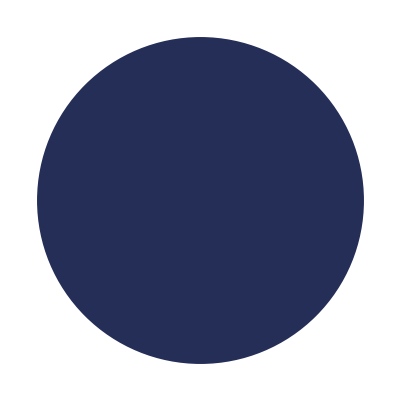
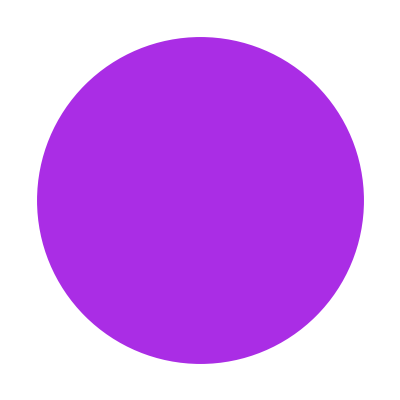
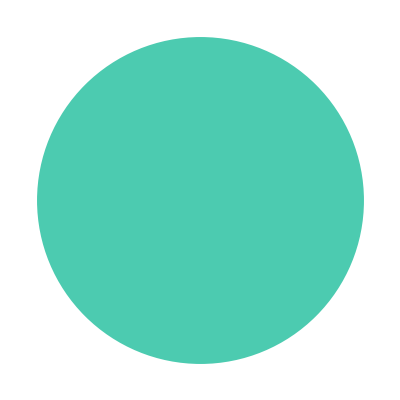
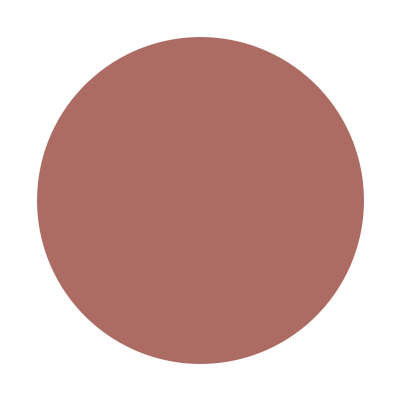
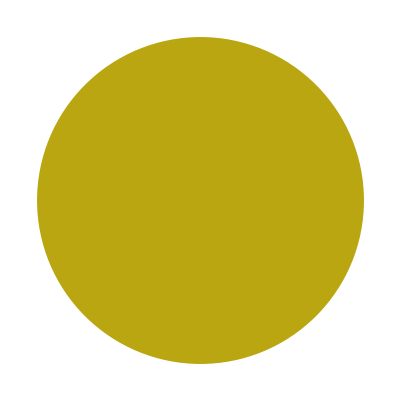
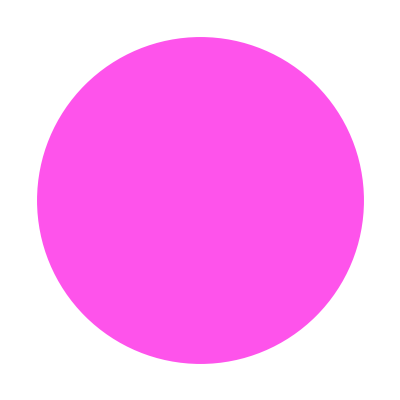
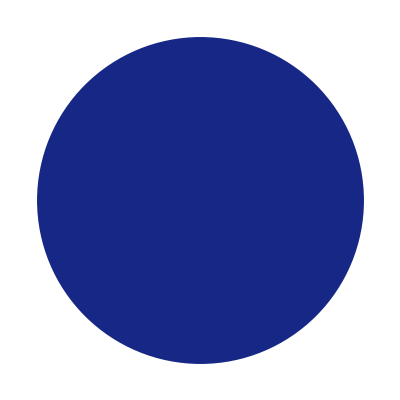
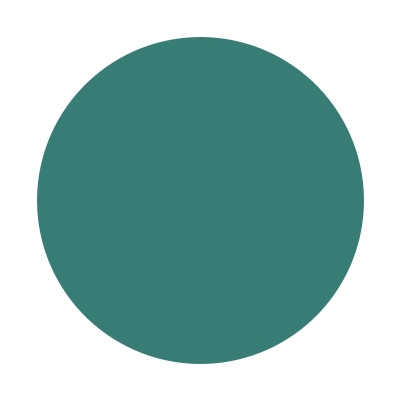

```mathematica
Graphics[{#,Disk[]}]&/@RandomColor[6 3]
```

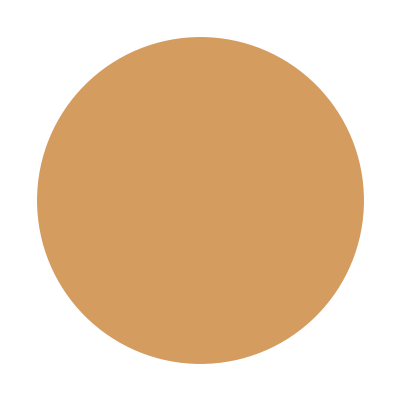
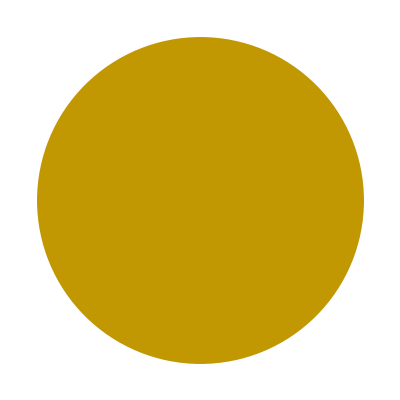
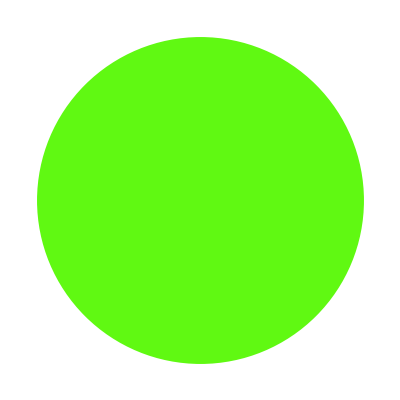
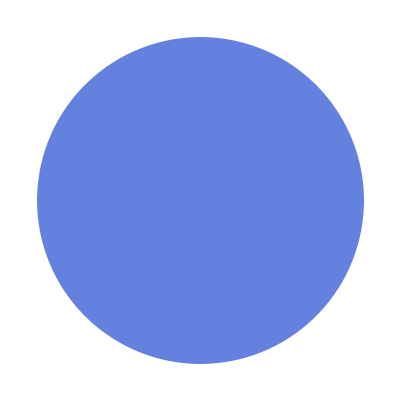
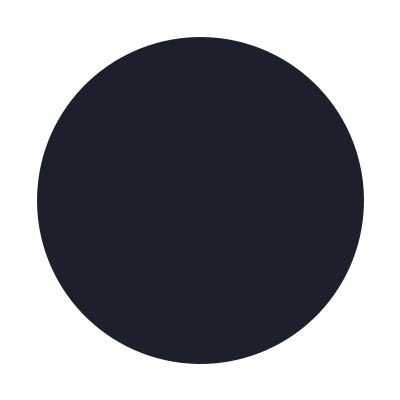
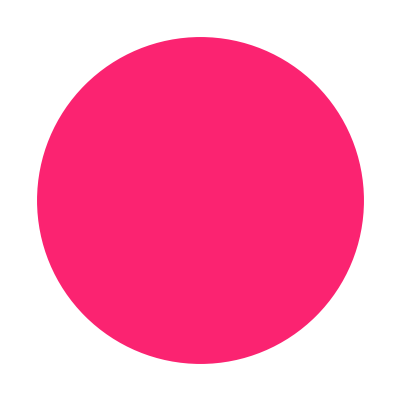
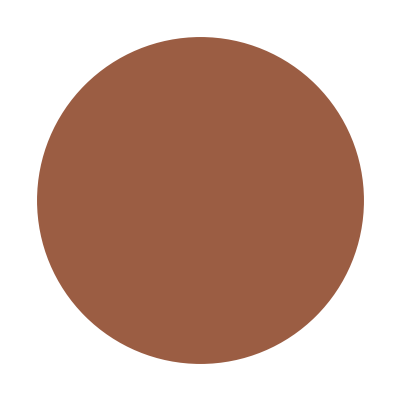
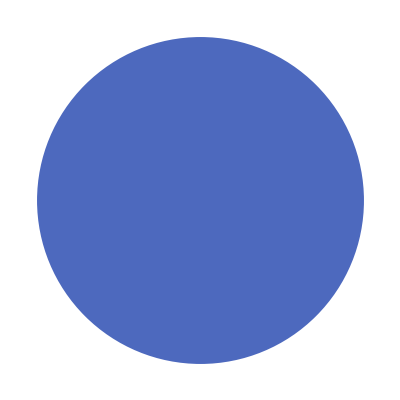
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[Graphics[{#,Disk[]}]&/@RandomColor[6 3]]
```

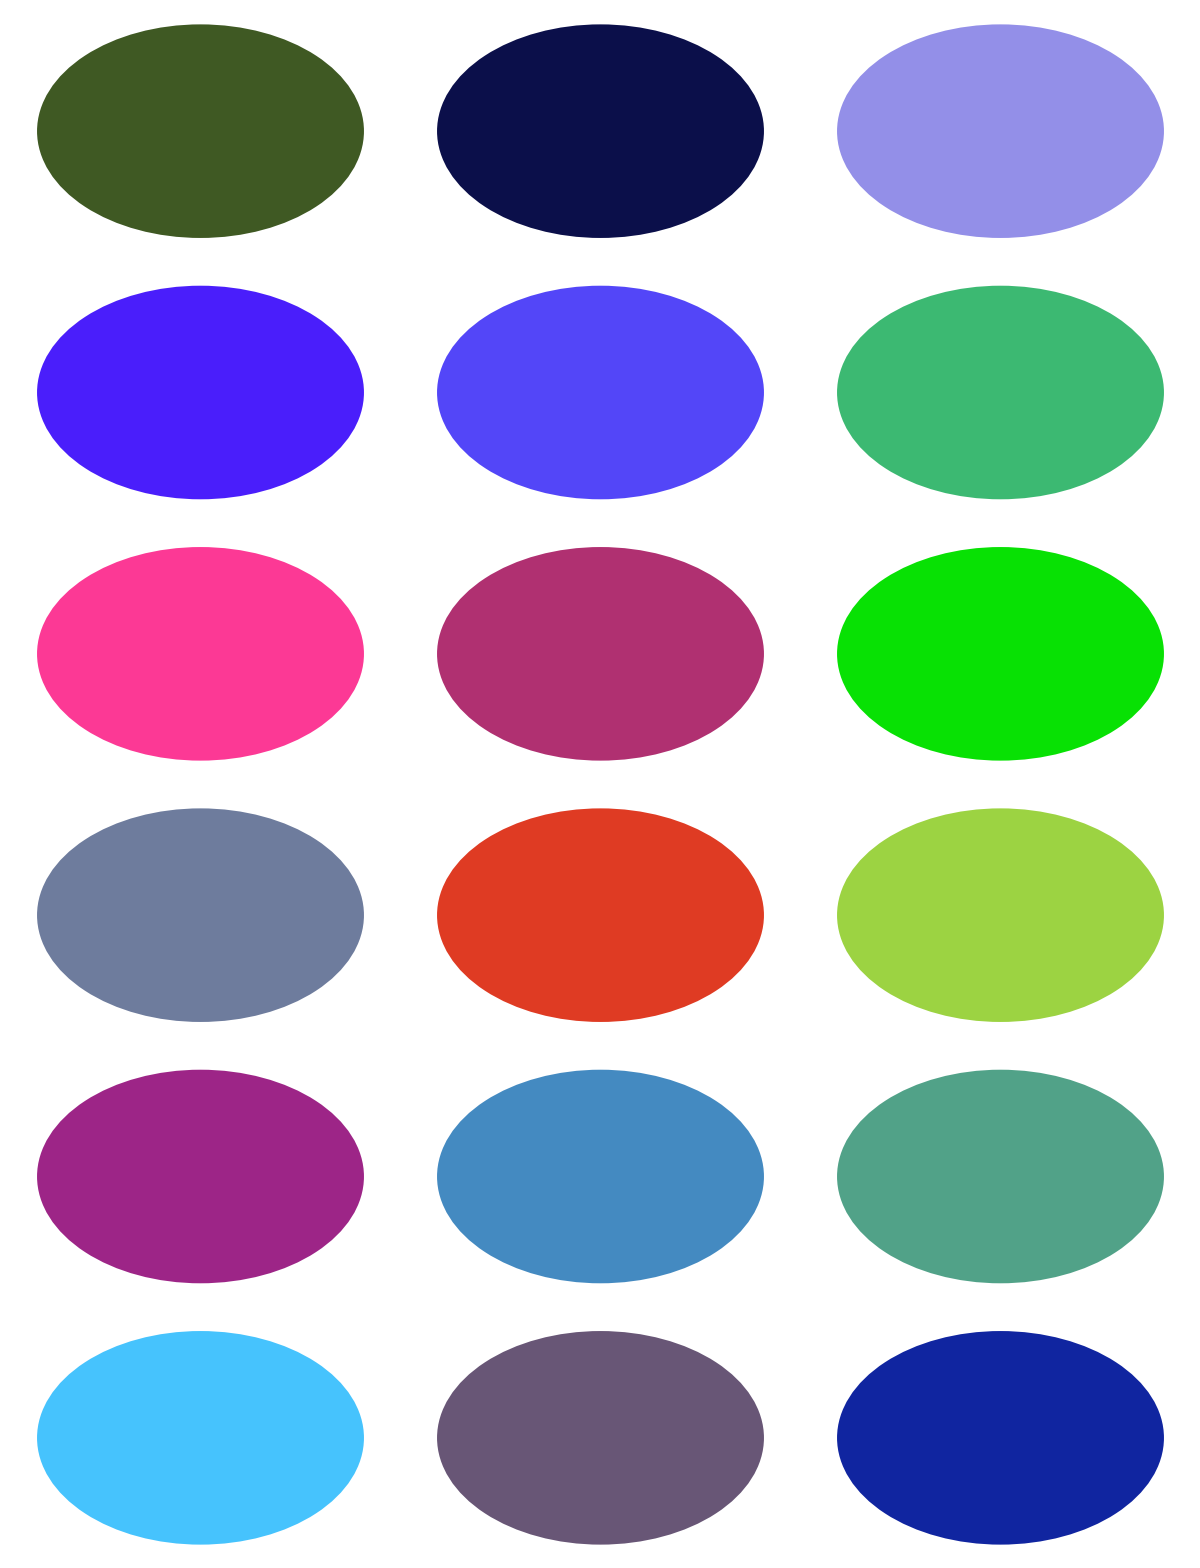

```mathematica
Multicolumn[Graphics[{#,Disk[]}]&/@RandomColor[6 3],{6,3}]
```

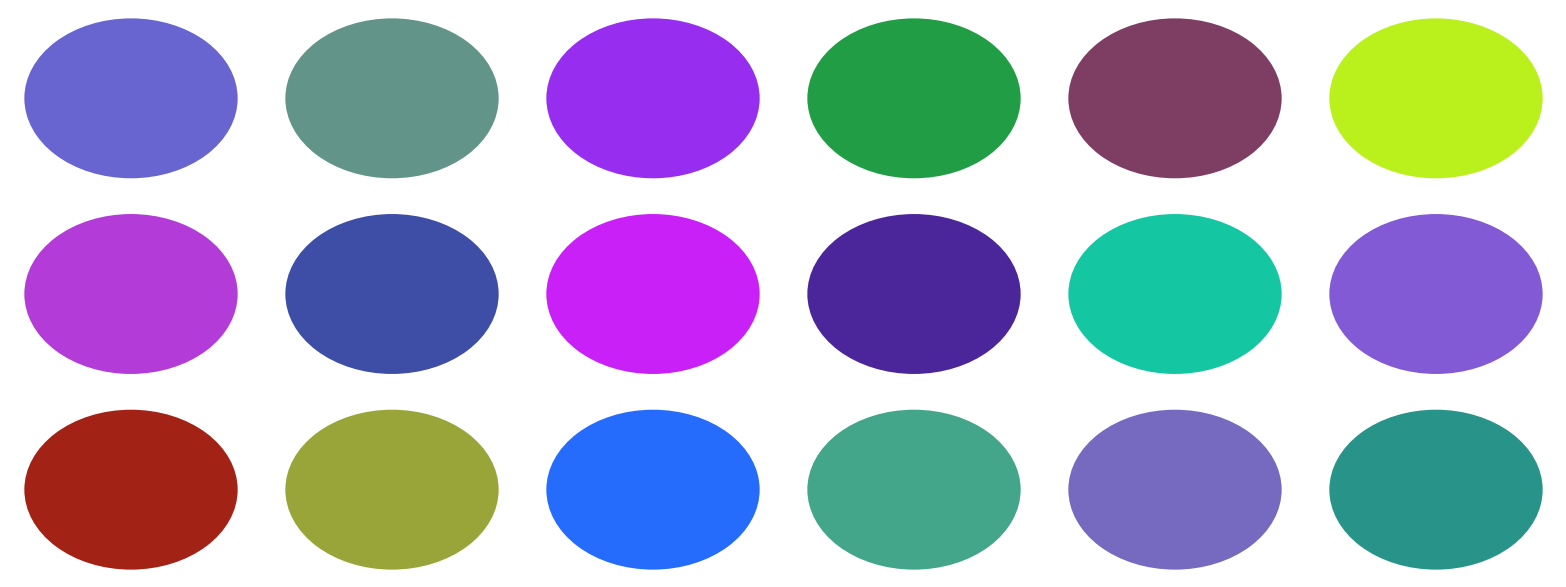

```mathematica
Multicolumn[Graphics[{#,Disk[]}]&/@RandomColor[6 3],{3,6}]
```

Make a 5×5 GraphicsGrid of pie charts that give the relative frequencies of digits in 2^n with n starting at 1

```mathematica
IntegerDigits[2^Range[10]]
```

{{2},{4},{8},{1,6},{3,2},{6,4},{1,2,8},{2,5,6},{5,1,2},{1,0,2,4}}

```mathematica
Counts/@IntegerDigits[2^Range[10]]
```

{<|2→1|>,<|4→1|>,<|8→1|>,<|1→1,6→1|>,<|3→1,2→1|>,<|6→1,4→1|>,<|1→1,2→1,8→1|>,<|2→1,5→1,6→1|>,<|5→1,1→1,2→1|>,<|1→1,0→1,2→1,4→1|>}

```mathematica
PieChart[Counts[#]]&/@IntegerDigits[2^Range[10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PieChart[Counts[#]]&/@IntegerDigits[2^Range[25]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Multicolumn[PieChart[Counts[#]]&/@IntegerDigits[2^Range[25]]]
```

-Graphics-

```mathematica
Multicolumn[PieChart[Counts[#]]&/@IntegerDigits[2^Range[25]],Appearance->"Horizontal"]
```

-Graphics-

Make a graphics row of word clouds for Wikipedia articles on the G5 countries.

```mathematica
WordCloud[WikipediaData[#]]&/@EntityList[EntityClass["Country","GroupOf20"]]
```

$Aborted

Use a pure function with constant arguments:

```mathematica
Map[f[#,3]&,{a,b,c}]
```

{f[a,3],f[b,3],f[c,3]}

### Apply

Display the factorization of an integer using superscripts:

```mathematica
FactorInteger[100!]
```

{{2,97},{3,48},{5,24},{7,16},{11,9},{13,7},{17,5},{19,5},{23,4},{29,3},{31,3},{37,2},{41,2},{43,2},{47,2},{53,1},{59,1},{61,1},{67,1},{71,1},{73,1},{79,1},{83,1},{89,1},{97,1}}

```mathematica
CenterDot@@(Superscript@@@FactorInteger[100!])
```

2^97·3^48·5^24·7^16·11^9·13^7·17^5·19^5·23^4·29^3·31^3·37^2·41^2·43^2·47^2·53^1·59^1·61^1·67^1·71^1·73^1·79^1·83^1·89^1·97^1

Create a table from a list of range specifications:

```mathematica
Table[i^j,##]&@@{{i,3},{j,5}}
```

{{1,1,1,1,1},{2,4,8,16,32},{3,9,27,81,243}}

```mathematica
Table[i^j,##]&@@{{i,10},{j,10}}
```

{{1,1,1,1,1,1,1,1,1,1},{2,4,8,16,32,64,128,256,512,1024},{3,9,27,81,243,729,2187,6561,19683,59049},{4,16,64,256,1024,4096,16384,65536,262144,1048576},{5,25,125,625,3125,15625,78125,390625,1953125,9765625},{6,36,216,1296,7776,46656,279936,1679616,10077696,60466176},{7,49,343,2401,16807,117649,823543,5764801,40353607,282475249},{8,64,512,4096,32768,262144,2097152,16777216,134217728,1073741824},{9,81,729,6561,59049,531441,4782969,43046721,387420489,3486784401},{10,100,1000,10000,100000,1000000,10000000,100000000,1000000000,10000000000}}

```mathematica
Grid[Table[i^j,##]&@@{{i,10},{j,10}}]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024
3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049
4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576
5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625
6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176
7 | 49 | 343 | 2401 | 16807 | 117649 | 823543 | 5764801 | 40353607 | 282475249
8 | 64 | 512 | 4096 | 32768 | 262144 | 2097152 | 16777216 | 134217728 | 1073741824
9 | 81 | 729 | 6561 | 59049 | 531441 | 4782969 | 43046721 | 387420489 | 3486784401
10 | 100 | 1000 | 10000 | 100000 | 1000000 | 10000000 | 100000000 | 1000000000 | 10000000000

```mathematica
TableForm[Table[i^j,##]&@@{{i,20},{j,20}}]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192 | 16384 | 32768 | 65536 | 131072 | 262144 | 524288 | 1048576
3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323 | 4782969 | 14348907 | 43046721 | 129140163 | 387420489 | 1162261467 | 3486784401
4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864 | 268435456 | 1073741824 | 4294967296 | 17179869184 | 68719476736 | 274877906944 | 1099511627776
5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125 | 6103515625 | 30517578125 | 152587890625 | 762939453125 | 3814697265625 | 19073486328125 | 95367431640625
6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016 | 78364164096 | 470184984576 | 2821109907456 | 16926659444736 | 101559956668416 | 609359740010496 | 3656158440062976
7 | 49 | 343 | 2401 | 16807 | 117649 | 823543 | 5764801 | 40353607 | 282475249 | 1977326743 | 13841287201 | 96889010407 | 678223072849 | 4747561509943 | 33232930569601 | 232630513987207 | 1628413597910449 | 11398895185373143 | 79792266297612001
8 | 64 | 512 | 4096 | 32768 | 262144 | 2097152 | 16777216 | 134217728 | 1073741824 | 8589934592 | 68719476736 | 549755813888 | 4398046511104 | 35184372088832 | 281474976710656 | 2251799813685248 | 18014398509481984 | 144115188075855872 | 1152921504606846976
9 | 81 | 729 | 6561 | 59049 | 531441 | 4782969 | 43046721 | 387420489 | 3486784401 | 31381059609 | 282429536481 | 2541865828329 | 22876792454961 | 205891132094649 | 1853020188851841 | 16677181699666569 | 150094635296999121 | 1350851717672992089 | 12157665459056928801
10 | 100 | 1000 | 10000 | 100000 | 1000000 | 10000000 | 100000000 | 1000000000 | 10000000000 | 100000000000 | 1000000000000 | 10000000000000 | 100000000000000 | 1000000000000000 | 10000000000000000 | 100000000000000000 | 1000000000000000000 | 10000000000000000000 | 100000000000000000000
11 | 121 | 1331 | 14641 | 161051 | 1771561 | 19487171 | 214358881 | 2357947691 | 25937424601 | 285311670611 | 3138428376721 | 34522712143931 | 379749833583241 | 4177248169415651 | 45949729863572161 | 505447028499293771 | 5559917313492231481 | 61159090448414546291 | 672749994932560009201
12 | 144 | 1728 | 20736 | 248832 | 2985984 | 35831808 | 429981696 | 5159780352 | 61917364224 | 743008370688 | 8916100448256 | 106993205379072 | 1283918464548864 | 15407021574586368 | 184884258895036416 | 2218611106740436992 | 26623333280885243904 | 319479999370622926848 | 3833759992447475122176
13 | 169 | 2197 | 28561 | 371293 | 4826809 | 62748517 | 815730721 | 10604499373 | 137858491849 | 1792160394037 | 23298085122481 | 302875106592253 | 3937376385699289 | 51185893014090757 | 665416609183179841 | 8650415919381337933 | 112455406951957393129 | 1461920290375446110677 | 19004963774880799438801
14 | 196 | 2744 | 38416 | 537824 | 7529536 | 105413504 | 1475789056 | 20661046784 | 289254654976 | 4049565169664 | 56693912375296 | 793714773254144 | 11112006825558016 | 155568095557812224 | 2177953337809371136 | 30491346729331195904 | 426878854210636742656 | 5976303958948914397184 | 83668255425284801560576
15 | 225 | 3375 | 50625 | 759375 | 11390625 | 170859375 | 2562890625 | 38443359375 | 576650390625 | 8649755859375 | 129746337890625 | 1946195068359375 | 29192926025390625 | 437893890380859375 | 6568408355712890625 | 98526125335693359375 | 1477891880035400390625 | 22168378200531005859375 | 332525673007965087890625
16 | 256 | 4096 | 65536 | 1048576 | 16777216 | 268435456 | 4294967296 | 68719476736 | 1099511627776 | 17592186044416 | 281474976710656 | 4503599627370496 | 72057594037927936 | 1152921504606846976 | 18446744073709551616 | 295147905179352825856 | 4722366482869645213696 | 75557863725914323419136 | 1208925819614629174706176
17 | 289 | 4913 | 83521 | 1419857 | 24137569 | 410338673 | 6975757441 | 118587876497 | 2015993900449 | 34271896307633 | 582622237229761 | 9904578032905937 | 168377826559400929 | 2862423051509815793 | 48661191875666868481 | 827240261886336764177 | 14063084452067724991009 | 239072435685151324847153 | 4064231406647572522401601
18 | 324 | 5832 | 104976 | 1889568 | 34012224 | 612220032 | 11019960576 | 198359290368 | 3570467226624 | 64268410079232 | 1156831381426176 | 20822964865671168 | 374813367582081024 | 6746640616477458432 | 121439531096594251776 | 2185911559738696531968 | 39346408075296537575424 | 708235345355337676357632 | 12748236216396078174437376
19 | 361 | 6859 | 130321 | 2476099 | 47045881 | 893871739 | 16983563041 | 322687697779 | 6131066257801 | 116490258898219 | 2213314919066161 | 42052983462257059 | 799006685782884121 | 15181127029874798299 | 288441413567621167681 | 5480386857784802185939 | 104127350297911241532841 | 1978419655660313589123979 | 37589973457545958193355601
20 | 400 | 8000 | 160000 | 3200000 | 64000000 | 1280000000 | 25600000000 | 512000000000 | 10240000000000 | 204800000000000 | 4096000000000000 | 81920000000000000 | 1638400000000000000 | 32768000000000000000 | 655360000000000000000 | 13107200000000000000000 | 262144000000000000000000 | 5242880000000000000000000 | 104857600000000000000000000

```mathematica
Manipulate[TableForm[Table[i^j,##]&@@{{i,n},{j,n}}],{n,4,20}]
```

Turn a function that takes several arguments into one that takes a list of arguments:

```mathematica
cplus[list_]:=Plus@@list
```

```mathematica
cplus[{a,b,c}]
```

a+b+c

```mathematica
cplus[{a,b,c,d,e,f,g}]
```

a+b+c+d+e+f+g

Find random co-prime integers:

```mathematica
Select[Apply[CoprimeQ]][RandomInteger[10,{20,2}]]
```

{{5,3},{7,6},{9,1},{1,2},{5,9},{9,1}}

```mathematica
?CoprimeQ
```

```mathematica
Select[Apply[CoprimeQ]][RandomInteger[10,{20,3}]]
```

{{1,1,2},{7,4,9},{4,9,5},{7,1,6}}

```mathematica
Select[Apply[CoprimeQ]][RandomInteger[1000,{1000,7}]]
```

{{166,655,857,943,541,557,59},{457,269,785,3,689,593,392},{757,832,237,421,263,527,575},{515,19,593,163,941,479,58},{857,463,547,616,1,705,181},{227,193,542,485,683,513,217}}

Check that the GCD is 1 for every case:

```mathematica
GCD@@@Select[Apply[CoprimeQ]][RandomInteger[1000,{1000,7}]]
```

{1,1,1,1,1,1}

### MapApply

Compute the angles with respect to the positive x axis for a list of ordered pairs:

```mathematica
ArcTan@@@{{1,1},{-1,1},{-1,-1},{1,-1}}
```

{π/4,(3 π)/4,-(3 π)/4,-π/4}

Display the factorization of an integer using superscripts:

```mathematica
FactorInteger[20!]
```

{{2,18},{3,8},{5,4},{7,2},{11,1},{13,1},{17,1},{19,1}}

```mathematica
CenterDot@@MapApply[Superscript,FactorInteger[20!]]
```

2^18·3^8·5^4·7^2·11^1·13^1·17^1·19^1

```mathematica
CenterDot@@Superscript@@@FactorInteger[20!]
```

2^18·3^8·5^4·7^2·11^1·13^1·17^1·19^1

```mathematica
CenterDot@@Superscript@@@FactorInteger[2022!]
```

2^2014·3^1006·5^503·7^334·11^200·13^166·17^124·19^111·23^90·29^71·31^67·37^55·41^50·43^48·47^43·53^38·59^34·61^33·67^30·71^28·73^27·79^25·83^24·89^22·97^20·101^20·103^19·107^18·109^18·113^17·127^15·131^15·137^14·139^14·149^13·151^13·157^12·163^12·167^12·173^11·179^11·181^11·191^10·193^10·197^10·199^10·211^9·223^9·227^8·229^8·233^8·239^8·241^8·251^8·257^7·263^7·269^7·271^7·277^7·281^7·283^7·293^6·307^6·311^6·313^6·317^6·331^6·337^6·347^5·349^5·353^5·359^5·367^5·373^5·379^5·383^5·389^5·397^5·401^5·409^4·419^4·421^4·431^4·433^4·439^4·443^4·449^4·457^4·461^4·463^4·467^4·479^4·487^4·491^4·499^4·503^4·509^3·521^3·523^3·541^3·547^3·557^3·563^3·569^3·571^3·577^3·587^3·593^3·599^3·601^3·607^3·613^3·617^3·619^3·631^3·641^3·643^3·647^3·653^3·659^3·661^3·673^3·677^2·683^2·691^2·701^2·709^2·719^2·727^2·733^2·739^2·743^2·751^2·757^2·761^2·769^2·773^2·787^2·797^2·809^2·811^2·821^2·823^2·827^2·829^2·839^2·853^2·857^2·859^2·863^2·877^2·881^2·883^2·887^2·907^2·911^2·919^2·929^2·937^2·941^2·947^2·953^2·967^2·971^2·977^2·983^2·991^2·997^2·1009^2·1013^1·1019^1·1021^1·1031^1·1033^1·1039^1·1049^1·1051^1·1061^1·1063^1·1069^1·1087^1·1091^1·1093^1·1097^1·1103^1·1109^1·1117^1·1123^1·1129^1·1151^1·1153^1·1163^1·1171^1·1181^1·1187^1·1193^1·1201^1·1213^1·1217^1·1223^1·1229^1·1231^1·1237^1·1249^1·1259^1·1277^1·1279^1·1283^1·1289^1·1291^1·1297^1·1301^1·1303^1·1307^1·1319^1·1321^1·1327^1·1361^1·1367^1·1373^1·1381^1·1399^1·1409^1·1423^1·1427^1·1429^1·1433^1·1439^1·1447^1·1451^1·1453^1·1459^1·1471^1·1481^1·1483^1·1487^1·1489^1·1493^1·1499^1·1511^1·1523^1·1531^1·1543^1·1549^1·1553^1·1559^1·1567^1·1571^1·1579^1·1583^1·1597^1·1601^1·1607^1·1609^1·1613^1·1619^1·1621^1·1627^1·1637^1·1657^1·1663^1·1667^1·1669^1·1693^1·1697^1·1699^1·1709^1·1721^1·1723^1·1733^1·1741^1·1747^1·1753^1·1759^1·1777^1·1783^1·1787^1·1789^1·1801^1·1811^1·1823^1·1831^1·1847^1·1861^1·1867^1·1871^1·1873^1·1877^1·1879^1·1889^1·1901^1·1907^1·1913^1·1931^1·1933^1·1949^1·1951^1·1973^1·1979^1·1987^1·1993^1·1997^1·1999^1·2003^1·2011^1·2017^1

```mathematica
CircleDot@@Superscript@@@FactorInteger[2022!]
```

2^2014⊙3^1006⊙5^503⊙7^334⊙11^200⊙13^166⊙17^124⊙19^111⊙23^90⊙29^71⊙31^67⊙37^55⊙41^50⊙43^48⊙47^43⊙53^38⊙59^34⊙61^33⊙67^30⊙71^28⊙73^27⊙79^25⊙83^24⊙89^22⊙97^20⊙101^20⊙103^19⊙107^18⊙109^18⊙113^17⊙127^15⊙131^15⊙137^14⊙139^14⊙149^13⊙151^13⊙157^12⊙163^12⊙167^12⊙173^11⊙179^11⊙181^11⊙191^10⊙193^10⊙197^10⊙199^10⊙211^9⊙223^9⊙227^8⊙229^8⊙233^8⊙239^8⊙241^8⊙251^8⊙257^7⊙263^7⊙269^7⊙271^7⊙277^7⊙281^7⊙283^7⊙293^6⊙307^6⊙311^6⊙313^6⊙317^6⊙331^6⊙337^6⊙347^5⊙349^5⊙353^5⊙359^5⊙367^5⊙373^5⊙379^5⊙383^5⊙389^5⊙397^5⊙401^5⊙409^4⊙419^4⊙421^4⊙431^4⊙433^4⊙439^4⊙443^4⊙449^4⊙457^4⊙461^4⊙463^4⊙467^4⊙479^4⊙487^4⊙491^4⊙499^4⊙503^4⊙509^3⊙521^3⊙523^3⊙541^3⊙547^3⊙557^3⊙563^3⊙569^3⊙571^3⊙577^3⊙587^3⊙593^3⊙599^3⊙601^3⊙607^3⊙613^3⊙617^3⊙619^3⊙631^3⊙641^3⊙643^3⊙647^3⊙653^3⊙659^3⊙661^3⊙673^3⊙677^2⊙683^2⊙691^2⊙701^2⊙709^2⊙719^2⊙727^2⊙733^2⊙739^2⊙743^2⊙751^2⊙757^2⊙761^2⊙769^2⊙773^2⊙787^2⊙797^2⊙809^2⊙811^2⊙821^2⊙823^2⊙827^2⊙829^2⊙839^2⊙853^2⊙857^2⊙859^2⊙863^2⊙877^2⊙881^2⊙883^2⊙887^2⊙907^2⊙911^2⊙919^2⊙929^2⊙937^2⊙941^2⊙947^2⊙953^2⊙967^2⊙971^2⊙977^2⊙983^2⊙991^2⊙997^2⊙1009^2⊙1013^1⊙1019^1⊙1021^1⊙1031^1⊙1033^1⊙1039^1⊙1049^1⊙1051^1⊙1061^1⊙1063^1⊙1069^1⊙1087^1⊙1091^1⊙1093^1⊙1097^1⊙1103^1⊙1109^1⊙1117^1⊙1123^1⊙1129^1⊙1151^1⊙1153^1⊙1163^1⊙1171^1⊙1181^1⊙1187^1⊙1193^1⊙1201^1⊙1213^1⊙1217^1⊙1223^1⊙1229^1⊙1231^1⊙1237^1⊙1249^1⊙1259^1⊙1277^1⊙1279^1⊙1283^1⊙1289^1⊙1291^1⊙1297^1⊙1301^1⊙1303^1⊙1307^1⊙1319^1⊙1321^1⊙1327^1⊙1361^1⊙1367^1⊙1373^1⊙1381^1⊙1399^1⊙1409^1⊙1423^1⊙1427^1⊙1429^1⊙1433^1⊙1439^1⊙1447^1⊙1451^1⊙1453^1⊙1459^1⊙1471^1⊙1481^1⊙1483^1⊙1487^1⊙1489^1⊙1493^1⊙1499^1⊙1511^1⊙1523^1⊙1531^1⊙1543^1⊙1549^1⊙1553^1⊙1559^1⊙1567^1⊙1571^1⊙1579^1⊙1583^1⊙1597^1⊙1601^1⊙1607^1⊙1609^1⊙1613^1⊙1619^1⊙1621^1⊙1627^1⊙1637^1⊙1657^1⊙1663^1⊙1667^1⊙1669^1⊙1693^1⊙1697^1⊙1699^1⊙1709^1⊙1721^1⊙1723^1⊙1733^1⊙1741^1⊙1747^1⊙1753^1⊙1759^1⊙1777^1⊙1783^1⊙1787^1⊙1789^1⊙1801^1⊙1811^1⊙1823^1⊙1831^1⊙1847^1⊙1861^1⊙1867^1⊙1871^1⊙1873^1⊙1877^1⊙1879^1⊙1889^1⊙1901^1⊙1907^1⊙1913^1⊙1931^1⊙1933^1⊙1949^1⊙1951^1⊙1973^1⊙1979^1⊙1987^1⊙1993^1⊙1997^1⊙1999^1⊙2003^1⊙2011^1⊙2017^1

```mathematica
CirclePlus@@Superscript@@@FactorInteger[2022!]
```

2^2014⊕3^1006⊕5^503⊕7^334⊕11^200⊕13^166⊕17^124⊕19^111⊕23^90⊕29^71⊕31^67⊕37^55⊕41^50⊕43^48⊕47^43⊕53^38⊕59^34⊕61^33⊕67^30⊕71^28⊕73^27⊕79^25⊕83^24⊕89^22⊕97^20⊕101^20⊕103^19⊕107^18⊕109^18⊕113^17⊕127^15⊕131^15⊕137^14⊕139^14⊕149^13⊕151^13⊕157^12⊕163^12⊕167^12⊕173^11⊕179^11⊕181^11⊕191^10⊕193^10⊕197^10⊕199^10⊕211^9⊕223^9⊕227^8⊕229^8⊕233^8⊕239^8⊕241^8⊕251^8⊕257^7⊕263^7⊕269^7⊕271^7⊕277^7⊕281^7⊕283^7⊕293^6⊕307^6⊕311^6⊕313^6⊕317^6⊕331^6⊕337^6⊕347^5⊕349^5⊕353^5⊕359^5⊕367^5⊕373^5⊕379^5⊕383^5⊕389^5⊕397^5⊕401^5⊕409^4⊕419^4⊕421^4⊕431^4⊕433^4⊕439^4⊕443^4⊕449^4⊕457^4⊕461^4⊕463^4⊕467^4⊕479^4⊕487^4⊕491^4⊕499^4⊕503^4⊕509^3⊕521^3⊕523^3⊕541^3⊕547^3⊕557^3⊕563^3⊕569^3⊕571^3⊕577^3⊕587^3⊕593^3⊕599^3⊕601^3⊕607^3⊕613^3⊕617^3⊕619^3⊕631^3⊕641^3⊕643^3⊕647^3⊕653^3⊕659^3⊕661^3⊕673^3⊕677^2⊕683^2⊕691^2⊕701^2⊕709^2⊕719^2⊕727^2⊕733^2⊕739^2⊕743^2⊕751^2⊕757^2⊕761^2⊕769^2⊕773^2⊕787^2⊕797^2⊕809^2⊕811^2⊕821^2⊕823^2⊕827^2⊕829^2⊕839^2⊕853^2⊕857^2⊕859^2⊕863^2⊕877^2⊕881^2⊕883^2⊕887^2⊕907^2⊕911^2⊕919^2⊕929^2⊕937^2⊕941^2⊕947^2⊕953^2⊕967^2⊕971^2⊕977^2⊕983^2⊕991^2⊕997^2⊕1009^2⊕1013^1⊕1019^1⊕1021^1⊕1031^1⊕1033^1⊕1039^1⊕1049^1⊕1051^1⊕1061^1⊕1063^1⊕1069^1⊕1087^1⊕1091^1⊕1093^1⊕1097^1⊕1103^1⊕1109^1⊕1117^1⊕1123^1⊕1129^1⊕1151^1⊕1153^1⊕1163^1⊕1171^1⊕1181^1⊕1187^1⊕1193^1⊕1201^1⊕1213^1⊕1217^1⊕1223^1⊕1229^1⊕1231^1⊕1237^1⊕1249^1⊕1259^1⊕1277^1⊕1279^1⊕1283^1⊕1289^1⊕1291^1⊕1297^1⊕1301^1⊕1303^1⊕1307^1⊕1319^1⊕1321^1⊕1327^1⊕1361^1⊕1367^1⊕1373^1⊕1381^1⊕1399^1⊕1409^1⊕1423^1⊕1427^1⊕1429^1⊕1433^1⊕1439^1⊕1447^1⊕1451^1⊕1453^1⊕1459^1⊕1471^1⊕1481^1⊕1483^1⊕1487^1⊕1489^1⊕1493^1⊕1499^1⊕1511^1⊕1523^1⊕1531^1⊕1543^1⊕1549^1⊕1553^1⊕1559^1⊕1567^1⊕1571^1⊕1579^1⊕1583^1⊕1597^1⊕1601^1⊕1607^1⊕1609^1⊕1613^1⊕1619^1⊕1621^1⊕1627^1⊕1637^1⊕1657^1⊕1663^1⊕1667^1⊕1669^1⊕1693^1⊕1697^1⊕1699^1⊕1709^1⊕1721^1⊕1723^1⊕1733^1⊕1741^1⊕1747^1⊕1753^1⊕1759^1⊕1777^1⊕1783^1⊕1787^1⊕1789^1⊕1801^1⊕1811^1⊕1823^1⊕1831^1⊕1847^1⊕1861^1⊕1867^1⊕1871^1⊕1873^1⊕1877^1⊕1879^1⊕1889^1⊕1901^1⊕1907^1⊕1913^1⊕1931^1⊕1933^1⊕1949^1⊕1951^1⊕1973^1⊕1979^1⊕1987^1⊕1993^1⊕1997^1⊕1999^1⊕2003^1⊕2011^1⊕2017^1

```mathematica
CircleTimes@@Superscript@@@FactorInteger[2022!]
```

2^2014⊗3^1006⊗5^503⊗7^334⊗11^200⊗13^166⊗17^124⊗19^111⊗23^90⊗29^71⊗31^67⊗37^55⊗41^50⊗43^48⊗47^43⊗53^38⊗59^34⊗61^33⊗67^30⊗71^28⊗73^27⊗79^25⊗83^24⊗89^22⊗97^20⊗101^20⊗103^19⊗107^18⊗109^18⊗113^17⊗127^15⊗131^15⊗137^14⊗139^14⊗149^13⊗151^13⊗157^12⊗163^12⊗167^12⊗173^11⊗179^11⊗181^11⊗191^10⊗193^10⊗197^10⊗199^10⊗211^9⊗223^9⊗227^8⊗229^8⊗233^8⊗239^8⊗241^8⊗251^8⊗257^7⊗263^7⊗269^7⊗271^7⊗277^7⊗281^7⊗283^7⊗293^6⊗307^6⊗311^6⊗313^6⊗317^6⊗331^6⊗337^6⊗347^5⊗349^5⊗353^5⊗359^5⊗367^5⊗373^5⊗379^5⊗383^5⊗389^5⊗397^5⊗401^5⊗409^4⊗419^4⊗421^4⊗431^4⊗433^4⊗439^4⊗443^4⊗449^4⊗457^4⊗461^4⊗463^4⊗467^4⊗479^4⊗487^4⊗491^4⊗499^4⊗503^4⊗509^3⊗521^3⊗523^3⊗541^3⊗547^3⊗557^3⊗563^3⊗569^3⊗571^3⊗577^3⊗587^3⊗593^3⊗599^3⊗601^3⊗607^3⊗613^3⊗617^3⊗619^3⊗631^3⊗641^3⊗643^3⊗647^3⊗653^3⊗659^3⊗661^3⊗673^3⊗677^2⊗683^2⊗691^2⊗701^2⊗709^2⊗719^2⊗727^2⊗733^2⊗739^2⊗743^2⊗751^2⊗757^2⊗761^2⊗769^2⊗773^2⊗787^2⊗797^2⊗809^2⊗811^2⊗821^2⊗823^2⊗827^2⊗829^2⊗839^2⊗853^2⊗857^2⊗859^2⊗863^2⊗877^2⊗881^2⊗883^2⊗887^2⊗907^2⊗911^2⊗919^2⊗929^2⊗937^2⊗941^2⊗947^2⊗953^2⊗967^2⊗971^2⊗977^2⊗983^2⊗991^2⊗997^2⊗1009^2⊗1013^1⊗1019^1⊗1021^1⊗1031^1⊗1033^1⊗1039^1⊗1049^1⊗1051^1⊗1061^1⊗1063^1⊗1069^1⊗1087^1⊗1091^1⊗1093^1⊗1097^1⊗1103^1⊗1109^1⊗1117^1⊗1123^1⊗1129^1⊗1151^1⊗1153^1⊗1163^1⊗1171^1⊗1181^1⊗1187^1⊗1193^1⊗1201^1⊗1213^1⊗1217^1⊗1223^1⊗1229^1⊗1231^1⊗1237^1⊗1249^1⊗1259^1⊗1277^1⊗1279^1⊗1283^1⊗1289^1⊗1291^1⊗1297^1⊗1301^1⊗1303^1⊗1307^1⊗1319^1⊗1321^1⊗1327^1⊗1361^1⊗1367^1⊗1373^1⊗1381^1⊗1399^1⊗1409^1⊗1423^1⊗1427^1⊗1429^1⊗1433^1⊗1439^1⊗1447^1⊗1451^1⊗1453^1⊗1459^1⊗1471^1⊗1481^1⊗1483^1⊗1487^1⊗1489^1⊗1493^1⊗1499^1⊗1511^1⊗1523^1⊗1531^1⊗1543^1⊗1549^1⊗1553^1⊗1559^1⊗1567^1⊗1571^1⊗1579^1⊗1583^1⊗1597^1⊗1601^1⊗1607^1⊗1609^1⊗1613^1⊗1619^1⊗1621^1⊗1627^1⊗1637^1⊗1657^1⊗1663^1⊗1667^1⊗1669^1⊗1693^1⊗1697^1⊗1699^1⊗1709^1⊗1721^1⊗1723^1⊗1733^1⊗1741^1⊗1747^1⊗1753^1⊗1759^1⊗1777^1⊗1783^1⊗1787^1⊗1789^1⊗1801^1⊗1811^1⊗1823^1⊗1831^1⊗1847^1⊗1861^1⊗1867^1⊗1871^1⊗1873^1⊗1877^1⊗1879^1⊗1889^1⊗1901^1⊗1907^1⊗1913^1⊗1931^1⊗1933^1⊗1949^1⊗1951^1⊗1973^1⊗1979^1⊗1987^1⊗1993^1⊗1997^1⊗1999^1⊗2003^1⊗2011^1⊗2017^1

### MapIndexed

Label parts by position:

```mathematica
MapIndexed[Labeled,{x^2,x+y,y^2,y^3}]
```

{x^2{1},x+y{2},y^2{3},y^3{4}}

```mathematica
MapIndexed[Framed[Labeled[#1,#2]]&,{x^2,x+y,y^2,y^3},Infinity]
```

{(x{1,1})^(2{1,2}){1},x{2,1}+y{2,2}{2},(y{3,1})^(2{3,2}){3},(y{4,1})^(3{4,2}){4}}

Use tooltips to show part numbers of subexpressions:

```mathematica
MapIndexed[Tooltip,Integrate[1/(x^4-1),x],Infinity]
```

-1/2 ArcTan[x]+-1/4 Log[1+x]+1/4 Log[1+-1 x]

Convert a list to a polynomial:

```mathematica
Total[MapIndexed[#1 x^First[#2]&,{a,b,c,d,e,f}]]
```

a x+b x^2+c x^3+d x^4+e x^5+f x^6

```mathematica
Total[MapIndexed[#1 x^First[#2]&,{a}]]
```

a x

```mathematica
Total[MapIndexed[#1 x^First[#2]&,{a,b}]]
```

a x+b x^2

```mathematica
Total[MapIndexed[#1 x^First[#2]&,{a,b,c}]]
```

a x+b x^2+c x^3

```mathematica
Total[MapIndexed[#1 x^First[#2]&,{a,b,c,d}]]
```

a x+b x^2+c x^3+d x^4

```mathematica
Total[MapIndexed[#1 x^(First[#2]-1)&,{a}]]
```

a

```mathematica
Total[MapIndexed[#1 x^(First[#2]-1)&,{a,b}]]
```

a+b x

```mathematica
Total[MapIndexed[#1 x^(First[#2]-1)&,{a,b,c}]]
```

a+b x+c x^2

```mathematica
Total[MapIndexed[#1 x^(First[#2]-1)&,Reverse[{a,b,c}]]]
```

c+b x+a x^2

Make the standard form of the quadratic equation:

```mathematica
Total[MapIndexed[#1 x^(First[#2]-1)&,Reverse[{a,b,c}]]]
```

c+b x+a x^2

Cubic polynomial:

```mathematica
Total[MapIndexed[#1 x^(First[#2]-1)&,Reverse[{a,b,c,d}]]]
```

d+c x+b x^2+a x^3

Quartic polynomial:

```mathematica
Total[MapIndexed[#1 x^(First[#2]-1)&,Reverse[{a,b,c,d,e}]]]
```

e+d x+c x^2+b x^3+a x^4

Rotate lists based on position:

```mathematica
MapIndexed[RotateLeft,Table[{a,b,c},{6}]]
```

{{b,c,a},{c,a,b},{a,b,c},{b,c,a},{c,a,b},{a,b,c}}

```mathematica
MapIndexed[RotateLeft,Table[{{a,b},{c,d}},{3},{3}],{2}]//MatrixForm
```

((d | c
b | a) | (c | d
a | b) | (d | c
b | a)
(b | a
d | c) | (a | b
c | d) | (b | a
d | c)
(d | c
b | a) | (c | d
a | b) | (d | c
b | a))

Obtain a list of all parts in an expression:

```mathematica
First@Last[Reap[MapIndexed[Sow[#2]&,{{a,b,c},{d},{{e}}},{1,∞}]]]
```

{{1,1},{1,2},{1,3},{1},{2,1},{2},{3,1,1},{3,1},{3}}

```mathematica
Position[{{a,b},{c},{{d}}},_,Infinity,Heads->False]
```

{{1,1},{1,2},{1},{2,1},{2},{3,1,1},{3,1},{3}}

### MapThread

Set up an outer totalistic cellular automaton:

```mathematica
t=RandomInteger[1,10]
```

{1,0,1,0,0,1,0,0,1,1}

```mathematica
MapThread[f,{t,RotateLeft[t]+RotateRight[t]}]
```

{f[1,1],f[0,2],f[1,0],f[0,1],f[0,1],f[1,0],f[0,1],f[0,1],f[1,1],f[1,2]}

Divide eigenvectors by their corresponding eigenvalues:

```mathematica
Eigensystem[{{1,3},{2,7}}]
```

{{4+√15,4-√15},{{1/2 (-3+√15),1},{1/2 (-3-√15),1}}}

```mathematica
MapThread[#2/#1&,Eigensystem[{{1,3},{2,7}}]]//FullSimplify
```

{{1/2 (-27+7 √15),4-√15},{1/2 (-27-7 √15),4+√15}}

Apply the functions in a list to corresponding arguments:

```mathematica
MapThread[#1@#2&,{{f,g,h},{x,y,z}}]
```

{f[x],g[y],h[z]}

## Neat Examples

Show nesting structure of an expression:

```mathematica
Integrate[1/(x^3-1),x]
```

-ArcTan[(1+2 x)/(√3)]/(√3)+1/3 Log[1-x]-1/6 Log[1+x+x^2]

```mathematica
Map[Framed,Integrate[1/(x^3-1),x],Infinity]
```

-1 ArcTan[3^(-1/2) 1+2 x] 3^(-1/2)+1/3 Log[1+-1 x]+-1/6 Log[1+x+x^2]

```mathematica
Map[Framed,Integrate[1/(x^11-1),x],Infinity]
```

-2/11 ArcTan[x+Sin[1/22 π] Sec[1/22 π]] Cos[1/22 π]+-2/11 ArcTan[x+-1 Sin[3/22 π] Sec[3/22 π]] Cos[3/22 π]+-2/11 ArcTan[x+Sin[5/22 π] Sec[5/22 π]] Cos[5/22 π]+1/11 Log[1+-1 x]+-1/11 Cos[1/11 π] Log[1+x^2+2 x Cos[1/11 π]]+1/11 Cos[2/11 π] Log[1+x^2+-2 x Cos[2/11 π]]+-1/11 Log[1+x^2+2 x Sin[1/22 π]] Sin[1/22 π]+-2/11 ArcTan[Csc[1/11 π] x+Cos[1/11 π]] Sin[1/11 π]+1/11 Log[1+x^2+-2 x Sin[3/22 π]] Sin[3/22 π]+-2/11 ArcTan[Csc[2/11 π] x+-1 Cos[2/11 π]] Sin[2/11 π]+-1/11 Log[1+x^2+2 x Sin[5/22 π]] Sin[5/22 π]

```mathematica
Integrate[1/(x^11-1),x]//TraditionalForm
```

-1/11 sin((5 π)/22) log(x^2+2 x sin((5 π)/22)+1)+1/11 sin((3 π)/22) log(x^2-2 x sin((3 π)/22)+1)-1/11 sin(π/22) log(x^2+2 x sin(π/22)+1)-1/11 cos(π/11) log(x^2+2 x cos(π/11)+1)+1/11 cos((2 π)/11) log(x^2-2 x cos((2 π)/11)+1)+1/11 log(1-x)-2/11 sin(π/11) tan^-1(csc(π/11) (x+cos(π/11)))-2/11 sin((2 π)/11) tan^-1(csc((2 π)/11) (x-cos((2 π)/11)))-2/11 cos((5 π)/22) tan^-1(sec((5 π)/22) (x+sin((5 π)/22)))-2/11 cos((3 π)/22) tan^-1(sec((3 π)/22) (x-sin((3 π)/22)))-2/11 cos(π/22) tan^-1(sec(π/22) (x+sin(π/22)))